```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
<<"handlebodies.m"
```

```mathematica
Geon[γ_,ρ_]:=(
InitializeHandlebody[];

AddCircle[{{0,0},ρ,"Inv"}];
AddCircle[{{Sec[γ],0},Tan[γ],"RU"}];

AddSymmetry["x"];AddSymmetry["y"];

SolveHandlebody[geon];

{2geon["BoundaryLengths"]⟦-1,1⟧,2geon["BoundaryLengths"]⟦1,1⟧,geon["Action"]}
)
```

```mathematica
Sec[γ]-Tan[γ]==ρ
```

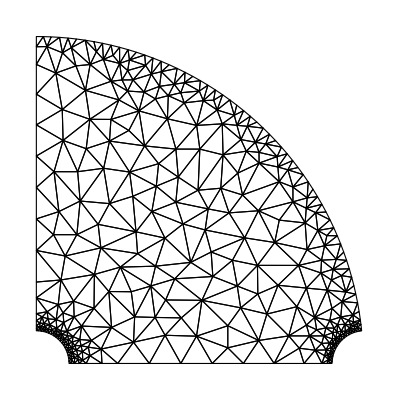

```mathematica
Geon[0.1,0.1];
geon["mesh"]["Wireframe"]
```

```mathematica
Dynamic[{γ,ρ}]
```

```mathematica
cache1=Flatten[Table[Table[Geon[γ,ρ],{ρ,0.05,Sec[γ]-Tan[γ]-0.05,0.05}],{γ,0.05,0.7,0.05}],1];
```

```mathematica
cache2=Flatten[Table[Table[Geon[γ,ρ],{ρ,0.01,0.07,0.01}],{γ,0.01,0.07,0.01}],1];
```

```mathematica
cache=cache1~Join~cache2;
```

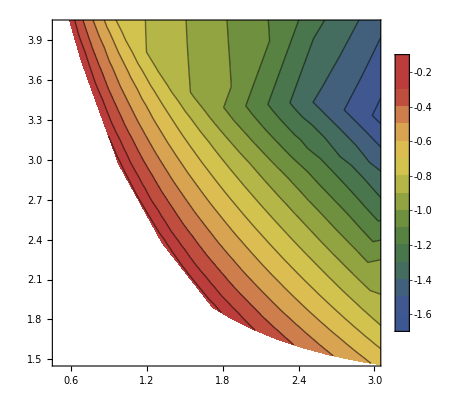

```mathematica
ListContourPlot[cache,ColorFunction->"DarkRainbow",PlotLegends->Automatic,Contours->15,PlotRange->{{0.5,3.0},{1.5,4}}]
```